```mathematica
(*Mathematica*)
```

```mathematica
(*scaled quantum gravity angles by dimension*)
```

```mathematica
a0={{2,28.74033889162101},{3,21.142008763446732},{4,19.47122063449069},{6,11.536959032815489},{10,7.414995869764551}}
```

{{2,28.7403},{3,21.142},{4,19.4712},{6,11.537},{10,7.415}}

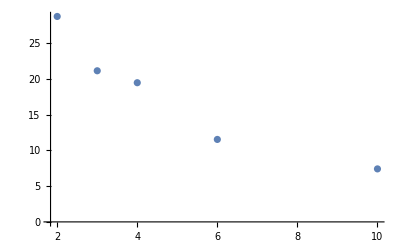

```mathematica
g1=ListPlot[a0]
```

```mathematica
f[x_]=Fit[a0,{1,x},x]
```

30.0816-2.48411 x

```mathematica
Solve[f[x]==43,x]
```

{{x→-5.2004}}

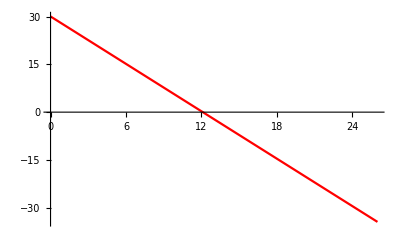

```mathematica
g2=Plot[f[x],{x,0,26},PlotStyle->Red]
```

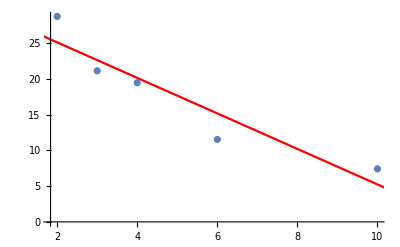

```mathematica
Show[{g1,g2}]
```

```mathematica
Solve[f[x]==0,x]
```

{{x→12.1096}}

```mathematica
Table[f[x],{x,0,26}]
```

{30.0816,27.5975,25.1134,22.6293,20.1452,17.6611,15.177,12.6929,10.2088,7.72467,5.24057,2.75646,0.272349,-2.21176,-4.69587,-7.17997,-9.66408,-12.1482,-14.6323,-17.1164,-19.6005,-22.0846,-24.5687,-27.0528,-29.5369,-32.0211,-34.5052}

```mathematica
(*at 4*Pi surface*)
```

```mathematica
Table[2*360/(f[x]*180/Pi),{x,0,12}]
```

{0.417742,0.455344,0.500385,0.555314,0.623789,0.711528,0.827988,0.990032,1.23094,1.62678,2.3979,4.55888,46.1406}

```mathematica
(*Polynomial output rank for dimensions SO(n) in Already unified solution for Higgs mmass*)
```

```mathematica
b0={{2,7},{3,9},{4,13},{5,17},{6,19},{7,22},{8,25},{9,28},{10,31},{11,35}}
```

{{2,7},{3,9},{4,13},{5,17},{6,19},{7,22},{8,25},{9,28},{10,31},{11,35}}

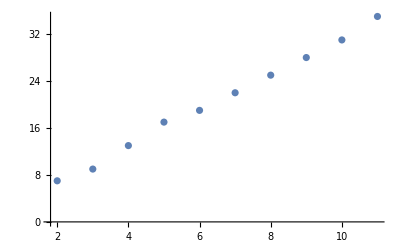

```mathematica
g3=ListPlot[b0]
```

```mathematica
Clear[g]
```

```mathematica
g[x_]=Fit[b0,{1,x},x]
```

0.587879+3.07879 x

```mathematica
g[26]
```

80.6364

```mathematica
Solve[g[x]==43,x]
```

{{x→13.7756}}

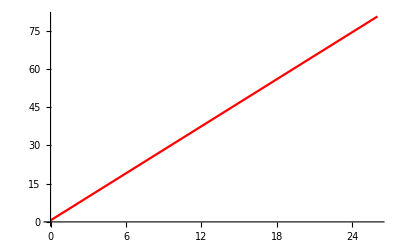

```mathematica
g4=Plot[g[x],{x,0,26},PlotStyle->Red]
```

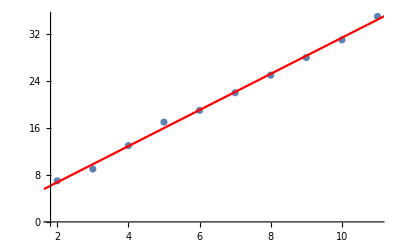

```mathematica
Show[{g3,g4}]
```

```mathematica
ParametricPlot3D[{x,Log[f[x]],Log[g[x]]},{x,0,26}]
```

-Graphics3D-

```mathematica
(*end*)
```